```mathematica
SetDirectory@NotebookDirectory[]
```

C:\Users\student\Documents\Cancer Bio Pics

```mathematica
si=Import["C:\\Users\\student\\Documents\\Cancer Bio Pics\\SiemensDataChart.csv"]
```

{{Day Number,Control,CRISPR/Cas9,Plasmid,Control,CRISPR/Cas9,Plasmid,Control,CRISPR/Cas9,Control,CRISPR/Cas9,Plasmid},{1,0.992188,0.997396,0.833333,0.994792,0.872396,0.888021,0.99349,0.934896,0.99349,0.934896,0.860677},{2,0.549479,0.283854,0.260417,0.458333,0.145833,0.223958,0.335938,0.682292,0.447917,0.37066,0.242188},{3,0.714844,0.163194,0.0846354,0.652344,0.140625,0.190104,0.375,0.169271,0.580729,0.157697,0.13737},{5,0.942708,0.00976563,0.192708,0.59375,0.00260417,0,0.626736,0.0611979,0.721065,0.0245226,0.0963542},{7,0.953125,0.00520833,0.00260417,0.458333,0.00520833,0.00651042,0.848958,0,0.753472,0.00347222,0.00455729}}

```mathematica
dates={{2017,12,8},{2017,12,9},{2017,12,10},{2017,12,12},{2017,12,14}}
```

{{2017,12,8},{2017,12,9},{2017,12,10},{2017,12,12},{2017,12,14}}

```mathematica
Dimensions[si]
```

{1,6,12}

```mathematica
days=Delete[si[[All,1]],1]
```

{1,2,3,5,7}

```mathematica
Table[{days[[i-1]],si[[1,i,5]]},{i,2,6}]
```

{{1.,0.994792},{2.,0.458333},{3.,0.652344},{5.,0.208333},{7.,0.0283565}}

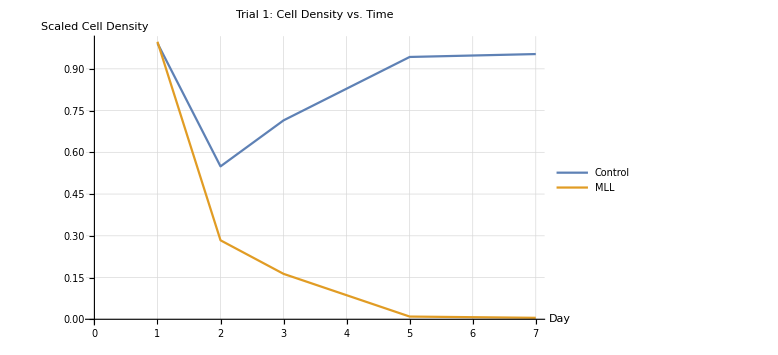

```mathematica
ListLinePlot[{Table[{days[[i-1]],si[[i,2]]},{i,2,6}],Table[{days[[i-1]],si[[i,3]]},{i,2,6}]},PlotLegends->{Style["Control",15,Black],Style["MLL",15,Black]},AxesLabel->{Style["Day",15, Black],Style["Scaled Cell Density",15, Black]},Frame->False,PlotLabel->Style["Trial 1: Cell Density vs. Time",17, Black],PlotTheme->"Detailed",Axes->True,ImageSize->Large]
```

```mathematica
Export["trial1np.png",#]&@%
```

trial1np.png

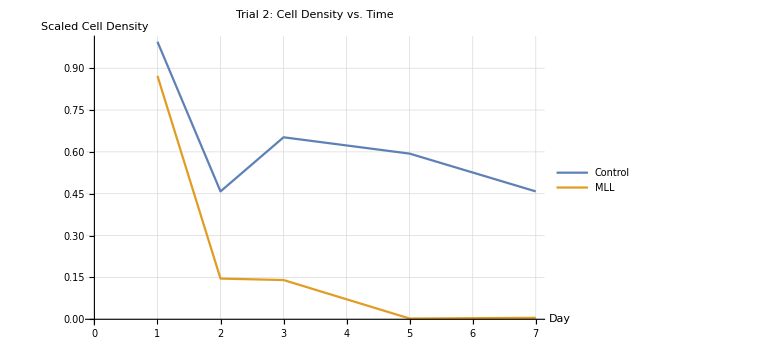

```mathematica
ListLinePlot[{Table[{days[[i-1]],si[[i,5]]},{i,2,6}],Table[{days[[i-1]],si[[i,6]]},{i,2,6}]},PlotLegends->{Style["Control",15,Black],Style["MLL",15,Black]},AxesLabel->{Style["Day",15, Black],Style["Scaled Cell Density",15, Black]},Frame->False,PlotLabel->Style["Trial 2: Cell Density vs. Time",17, Black],PlotTheme->"Detailed",Axes->True,ImageSize->Large]
```

```mathematica
Export["trial2np.png",#]&@%
```

trial2np.png

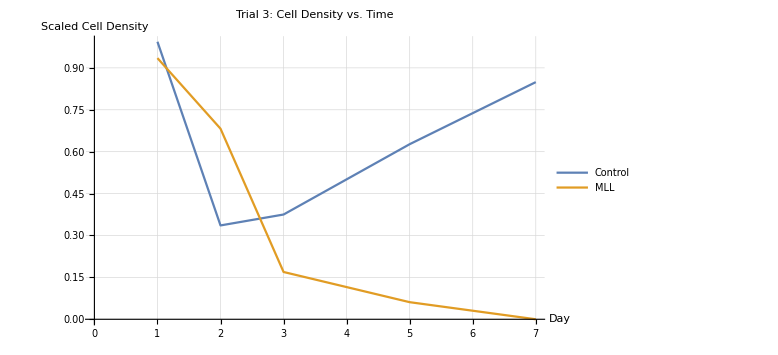

```mathematica
ListLinePlot[{Table[{days[[i-1]],si[[i,8]]},{i,2,6}],Table[{days[[i-1]],si[[i,9]]},{i,2,6}]},PlotLegends->{Style["Control",15,Black],Style["MLL",15,Black]},AxesLabel->{Style["Day",15, Black],Style["Scaled Cell Density",15, Black]},Frame->False,PlotLabel->Style["Trial 3: Cell Density vs. Time",17, Black],PlotTheme->"Detailed",Axes->True,ImageSize->Large]
```

```mathematica
Export["trial3np.png",#]&@%
```

trial3np.png

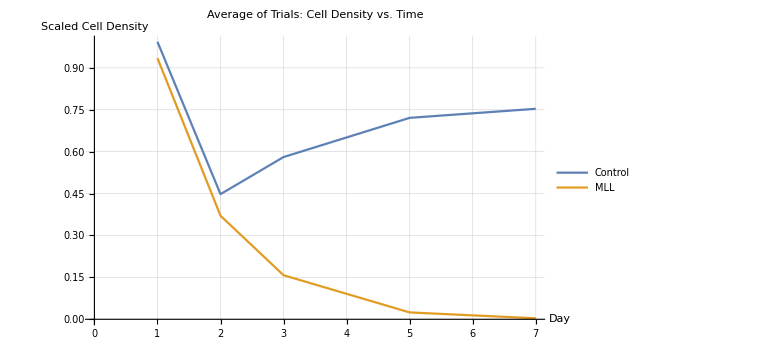

```mathematica
ListLinePlot[{Table[{days[[i-1]],si[[i,10]]},{i,2,6}],Table[{days[[i-1]],si[[i,11]]},{i,2,6}]},PlotLegends->{Style["Control",15,Black],Style["MLL",15,Black]},AxesLabel->{Style["Day",15, Black],Style["Scaled Cell Density",15, Black]},Frame->False,PlotLabel->Style["Average of Trials: Cell Density vs. Time",17, Black],PlotTheme->"Detailed",Axes->True,ImageSize->Large]
```

```mathematica
Export["averageNP.png",#]&@%
```

averageNP.png